# Math 385 HW # 2

## Mario L. Gutierrez Abed

Given f(x)=sin(x)ⅇ^-x, start with the seed x_0= 2.0. Then 
(1) Plot f(x) on [2,4]
(2) Use Newton’s method to find the root near π. 
(3) Compare with the answer you get from FindRoot[]

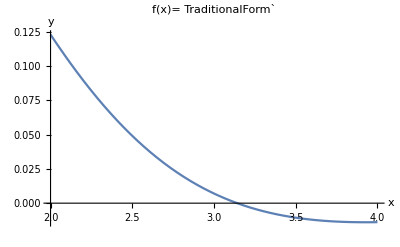

```mathematica
f[x_]=ⅇ^-x Sin[x];
Plot[f[x],{x,2,4},PlotLabel->Style["f(x)= TraditionalForm`",FontSize->14,FontColor->Purple],AxesLabel->{x,y}]
```

The tangent line at x_0 is given by f'(x_0)=(y - f(x_0))/(x - x_0). Now setting y=0 and then solving for x we have
            x=(f'(x_0)x_0 - f(x_0))/(f'(x_0)).
Now let’s use Newton’s method to find a root near π starting at the seed x_0=2 :

```mathematica
f[x_]=ⅇ^-x Sin[x];
g[x_]= D[f[x],x];
Subscript[x, 0]=2.0;
count = 0;
While[Abs[f[Subscript[x, 0]]]> 10^-5,
Subscript[x, 0] = (g[Subscript[x, 0]]*Subscript[x, 0] - f[Subscript[x, 0]])/g[Subscript[x, 0]];
count++
];
Subscript[x, 0]
count
```

3.14141

4

Thus 3.14141 is the root that we found near π iterating  Newton’s method four times. Now we use the FindRoot built-in function :

```mathematica
realans = FindRoot[f[x],{x,2.0}];
realans = realans⟦1⟧⟦2⟧
```

3.14159

We can see that the outputs differ after the third decimal. The absolute error associated with the two outputs is

```mathematica
Abs[Subscript[x, 0] - realans]//ScientificForm
```

1.84772×10^-4